```mathematica
Clear[interPP,isumPP ,isumZP,isumZZ,isumWW,isumWWdyt]
SetDirectory[NotebookDirectory[]];
interPP = Get["intang_PPtt_10TeV_fix.txt"];
interZP = Get["intang_ZPtt_10TeV_fix.txt"];
```

```mathematica
interWW = Get["intang_WWtt1.txt"];
interZZ = Get["intang_ZZtt_10TeV_Fix.txt"];
```



```mathematica
(*benchmarklist={3,4,5,7,8,10,11};*)
ColorData[24,"Image"]
(*ColorData[109,"Image"]*)
colorselecitonumber=24;
```

```mathematica
energygrid=Grid[{Table[Style[If[j==1,{"(√s= 3,","6,","10,","14,","30,","100 TeV)"}[[i]],"TeV"],If[j≠0,ColorData[colorselecitonumber][i]],Bold],{j,1,2,1},{i,1,6,1}][[1]]},Spacings->{0.5,0}]
```

(√s= 3, | 6, | 10, | 14, | 30, | 100 TeV)

```mathematica
dytinterWW = Get["intang_WWttDYT_10TeV_2dyt_new.txt"];
```

```mathematica
dytinterWWex= Get["intang_WWttDYT_10TeV_3.txt"];
dytinterWW11= Get["intang_WWttDYT11_10TeV_2dyt.txt"];
dytinterWW11ex= Get["intang_WWttDYT11_10TeV_dyt.txt"];
dytinterWWm1m1= Get["intang_WWttDYTm1m1_10TeV_2dyt.txt"];
dytinterWWm1m1ex= Get["intang_WWttDYTm1m1_10TeV_dyt.txt"];
dytinterZZ = Get["intang_ZZtt00DYT_10TeV_3_new.txt"];
dytinterZZ11= Get["intang_ZZtt11DYT_10TeV_3.txt"];
dytinterZZm1m1= Get["intang_ZZttm1m1DYT_10TeV_3.txt"];
dytt = Table[(1/10000)*(30i-300),{i,0,20}]
```

{-3/100,-27/1000,-3/125,-21/1000,-9/500,-3/200,-3/250,-9/1000,-3/500,-3/1000,0,3/1000,3/500,9/1000,3/250,3/200,9/500,21/1000,3/125,27/1000,3/100}

```mathematica
dytt[[11]]
```

0

```mathematica
angenPP[ang_,num_] :=interPP[[ang]] [(1 + ((num - 350)/50))]

angenZP[ang_,num_] :=interZP[[ang]] [(1 + ((num - 350)/50))]

angenWW[ang_,num_] :=interWW[[ang]][(1 + ((num - 350)/50))]

angenZZ[ang_,num_] :=interZZ[[ang]][(1 + ((num - 350)/50))]
```

```mathematica
isumWWdyt[ang_,dyt_,energy_] :=dytinterWW[[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterWW[[ang,11]][(1 + ((energy - 350)/50))]
```

```mathematica
isumWWdytex[ang_,dyt_,energy_] :=dytinterWWex[[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterWW[[ang,11]][(1 + ((energy - 350)/50))]
```

```mathematica
isumWWdyt11[ang_,dyt_,energy_] :=dytinterWW11[[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterWW11[[ang,11]][(1 + ((energy - 350)/50))]
```

```mathematica
isumWWdyt11ex[ang_,dyt_,energy_] :=dytinterWW11ex[[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterWW11[[ang,11]][(1 + ((energy - 350)/50))]
```

```mathematica
isumWWdytm1m1[ang_,dyt_,energy_] :=dytinterWWm1m1[[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterWWm1m1[[ang,11]][(1 + ((energy - 350)/50))]
```

```mathematica
isumWWdytm1m1ex[ang_,dyt_,energy_] :=dytinterWWm1m1ex[[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterWWm1m1[[ang,11]][(1 + ((energy - 350)/50))]
```

```mathematica
isumZZdyt00[ang_,dyt_,energy_] :=dytinterZZ[[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterZZ[[ang,11]][(1 + ((energy - 350)/50))]
```

```mathematica
isumZZdyt11[ang_,dyt_,energy_] :=dytinterZZ11[[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterZZ11[[ang,11]][(1 + ((energy - 350)/50))]
```

```mathematica
isumZZdytm1m1[ang_,dyt_,energy_] :=dytinterZZm1m1[[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterZZm1m1[[ang,11]][(1 + ((energy - 350)/50))]
```

```mathematica
isumWWdyt[4,12,500]
```

-0.0031659

```mathematica
isumWWdytex[4,12,500] *2
```

-0.00318163

```mathematica
isumWWdytm1m1[4,12,500]
```

0.0000228893

```mathematica
isumWWdytm1m1ex[4,12,500] *2
```

0.0000228426

```mathematica
isumWWdyt11[4,12,500] 
isumWWdyt11ex[4,12,500]
```

0.0000228893

0.0000114213

```mathematica
lum = 10;
sqrtsbin = Table[350 + 50*i, {i,0,194}];
br = N[72/81];
```

```mathematica
background = Table[NIntegrate[br*lum*(angenPP[k,ss]+angenWW[k,ss]+angenZP[k,ss]+angenZZ[k,ss]),{ss,sqrtsbin[[i]],sqrtsbin[[i+1]]}],{i,1,53},{k,1,18}];
```

```mathematica
signal = Table[NIntegrate[br*lum*((1*(isumWWdytex[k,j,ss]+isumWWdyt11ex[k,j,ss]+isumWWdytm1m1ex[k,j,ss]))+(1*(isumZZdyt00[k,j,ss]+isumZZdyt11[k,j,ss]+isumZZdytm1m1[k,j,ss]))),{ss,sqrtsbin[[i]],sqrtsbin[[i+1]]}],{i,1,53},{k,1,18},{j,1,Length@dytt}]
(*+isumZZdyt00[k,j,ss]+isumZZdyt11[k,j,ss]+isumZZdytm1m1[k,j,ss]*)
(*isumWWdyt[k,j,ss]+isumWWdyt11[k,j,ss]+isumWWdytm1m1[k,j,ss]*)
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

$Aborted

```mathematica
(*Sum angles*)
sumanglesbkg = Table[Sum[background[[i,n]],{n,1,18}],{i,1,53}];
sumanglessig = Table[Sum[signal[[i,n,j]],{n,1,18}],{i,1,53},{j,1,Length@dytt}];
```

```mathematica
sqrtsumanglesbkg =Sqrt[sumanglesbkg];
```

```mathematica
background1 = Table[NIntegrate[br*lum*(angenPP[k,ss]+angenWW[k,ss]+angenZP[k,ss]+angenZZ[k,ss]),{ss,3000,10000}],{k,1,18}];
```

```mathematica
signal1 = Table[NIntegrate[br*lum*((1*(isumWWdyt[k,j,ss]+isumWWdyt11[k,j,ss]+isumWWdytm1m1[k,j,ss]))+(1*(isumZZdyt00[k,j,ss]+isumZZdyt11[k,j,ss]+isumZZdytm1m1[k,j,ss]))),{ss,3000,10000}],{k,1,18},{j,1,Length@dytt}];
(*+isumZZdyt11[k,j,ss]+isumZZdytm1m1[k,j,ss]+isumZZdyt00[k,j,ss]*)
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

```mathematica
zzzz1 = Sum[sumanglesbkg[[i]],{i,1,53}] + sumanglesbkg1
```

406373.+sumanglesbkg1

```mathematica
zzzz/zzzz1
```

zzzz/(406373.+sumanglesbkg1)

```mathematica
(*Sum angles*)
sumanglesbkg1 = Sum[background1[[n]],{n,1,18}];
sumanglessig1 = Table[Sum[signal1[[n,j]],{n,1,18}],{j,1,Length@dytt}];
sqrtsumanglesbkg1 =Sqrt[sumanglesbkg1];
```

```mathematica
chi2sumang = Table[Sum[(sumanglessig [[i,j]]/sqrtsumanglesbkg [[i]])^2,{i,1,53}],{j,1,Length@dytt}];
```

```mathematica
chi2sumang1 = Table[(sumanglessig1 [[j]]/sqrtsumanglesbkg1)^2,{j,1,Length@dytt}];
```

```mathematica
chi = chi2sumang +chi2sumang1 ;
```

```mathematica
dytt = Table[(1/10000)*(30i-300),{i,0,20}]
dytchi2en = Table[{dytt[[k]],chi[[k]]},{k,1,Length@dytt}];
intdytchi2en = Interpolation[dytchi2en ]
sig1= Table[{dytt[[k]],1},{k,1,Length@dytt}];
```

{-3/100,-27/1000,-3/125,-21/1000,-9/500,-3/200,-3/250,-9/1000,-3/500,-3/1000,0,3/1000,3/500,9/1000,3/250,3/200,9/500,21/1000,3/125,27/1000,3/100}

InterpolatingFunction[…]

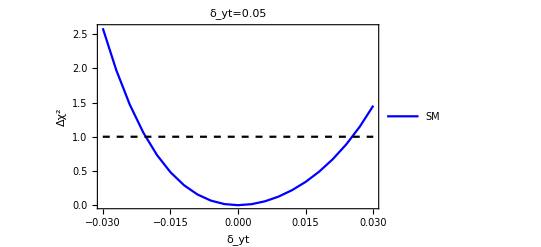

```mathematica
ListPlot[{intdytchi2en ,sig1},Joined->True,Frame->True,PlotStyle->{Blue,{Dashed,Black}},PlotLabel->Style["δ_yt=0.05",Black,20],PlotLegends->{"SM"},FrameLabel->{Style["δ_yt",Black,20],Style["Δχ^2",Black,15]},FrameTicksStyle->Directive[Black,13]]
```

```mathematica
(*bin angle and energy*)
sqrtback = Sqrt[background];
chi2 = Table[Sum[(signal[[i,j,k]]/ sqrtback[[i,j]])^2,{i,1,33},{j,2,17}],{k,1,Length@dytt}];
```

```mathematica
chi22 = Table[Sum[(signal[[i,j,k]]/ sqrtback[[i,j]])^2,{i,1,33},{j,1,18}],{k,1,Length@dytt}];
```

```mathematica
chi2
```

{6.51841,5.14297,3.95811,2.95176,2.11238,1.42893,0.890872,0.488201,0.211409,0.0515025,0.,0.048931,0.190836,0.418769,0.726292,1.10748,1.55692,2.06971,2.64146,3.26829,3.94684}

```mathematica
chi22-chi2
```

{0.156263,0.126763,0.100313,0.0769247,0.0566087,0.0393778,0.0252453,0.0142257,0.00633403,0.00158646,0.,0.00159258,0.00638305,0.0143911,0.0256375,0.0401437,0.0579322,0.0790264,0.103451,0.13123,0.162391}

```mathematica
dytchi2enang = Table[{dytt[[k]],chi2 [[k]]},{k,1,Length@dytt}];
intdytchi2enang = Interpolation[dytchi2enang ]
sig1= Table[{dytt[[k]],1},{k,1,Length@dytt}];
```

InterpolatingFunction[…]

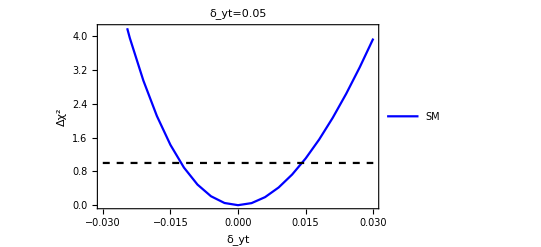

```mathematica
ListPlot[{intdytchi2enang ,sig1},Joined->True,Frame->True,PlotStyle->{Blue,{Dashed,Black}},PlotLabel->Style["δ_yt=0.05",Black,20],PlotLegends->{"SM"},FrameLabel->{Style["δ_yt",Black,20],Style["Δχ^2",Black,15]},FrameTicksStyle->Directive[Black,13]]
```

```mathematica
dyttnew = Table[(1/10000)*(i-300),{i,0,600}];
```

```mathematica
linear=Table[5577.209434254114dyttnew[[i]]^2,{i,1,601}];
```

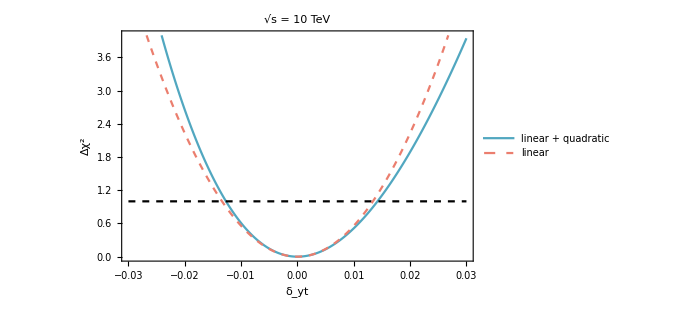

```mathematica
lineplot=ListPlot[{Transpose[{ dyttnew ,intdytchi2enang [dyttnew]}] , sig1,Transpose[{ dyttnew ,linear}]},Joined->True,PlotStyle->{ColorData[colorselecitonumber][5],{Dashed,Black},{Dashed,ColorData[colorselecitonumber][1]}},Frame->True,FrameLabel->{Style[DisplayForm["δ_yt"],Black,20,FontFamily->"Times"],Style["Δχ^2",Black,19,FontFamily->"Times"]},
PlotLabel->Style[DisplayForm[SqrtBox["s"] ]  Row[{" = ",10 TeV}]  ,Black,18,FontFamily->"Times"],
PlotLegends->Placed[LineLegend[{Directive[ColorData[colorselecitonumber][5]],Directive[ColorData[colorselecitonumber][1],Dashed]},{Style["linear + quadratic",FontFamily->"Times",15],Style["linear",FontFamily->"Times",15]}],{0.70,0.85}],
PlotRange->{{-0.03,0.03},{0,4}},
FrameTicksStyle->Directive[Black,17],ImageSize->500]
```

```mathematica
Export["chi_square_10TeV_angle_dilepton_out.pdf",lineplot]
```

chi_square_10TeV_angle_dilepton_out.pdf

```mathematica
data = Transpose[{ dyttnew ,intdytchi2enang [dyttnew]}];
```

```mathematica
b = Fit[data, {x^2,x^3,x^4},x]
```

5577.21 x^2-47621.7 x^3+263149. x^4

```mathematica
(*WW+ZZ
5577.209434254114``-47621.65161264546``+263149.3631429499``
WW
6232.5985458026735`` -46887.23987428005+213594.45151787635``
ZZ
101.77273442906788 +435.5871721715917+2582.497207032436
2WW+ZZ
23517.209324775296`-369060+3.6079833791653924*^6

*)
```

```mathematica
6232.5985458026735`+101.77273442906788-5577.209434254114
```

655.389

```mathematica
263149.3631429499-213594.45151787635-2582.497207032436
```

46972.4

```mathematica
-47621.65161264546+46887.23987428005 -435.5871721715917
```

-1170.

```mathematica
-369060 +(8*46887.23987428005)-435.5871721715917
```

5602.33

```mathematica
a- b= -1169.998910537
2a- b=5602.3318220688125/2
```

Set::write: Tag Plus in a+(-5577.21 x^2+47621.7 x^3-263149. x^4) is Protected.

-1108.42

Set::write: Tag Plus in 2 a+(-5577.21 x^2+47621.7 x^3-263149. x^4) is Protected.

835.262

```mathematica
a =  5602.3318220688125/2+1169.998910537
```

3971.16

```mathematica
b=3971.1648215714063+1169.998910537
```

5141.16

```mathematica
-(5141.163732108406*2) + (4*3971.1648215714063)
```

5602.33

```mathematica
3971.1648215714063-5141.163732108406
```

-1170.

```mathematica
Clear[z]
```

```mathematica
b=(5600z^2-48000z^3+260000z^4)//.z->-0.0127
```

1.00831

```mathematica
(5600z^2)//.z->-0.0133
```

0.990584

```mathematica
dyttnew[[601]];
```

Part::partw: Part 602 of {-3/100,-299/10000,-149/5000,-297/10000,-37/1250,-59/2000,-147/5000,-293/10000,-73/2500,-291/10000,«591»} does not exist.

```mathematica
0.0143
```

```mathematica
Clear[z]
```

```mathematica
(6232.5985458026735z^2-46887.23987428005z^3+213594.45151787635z^4) //.z-> -0.012
```

0.982944